## Peocesamiento de los datos de piel normal usando mcml con fuente paralela

Datos iniciales y abriendo el fichero

```mathematica
Nr=50;Nz=40;dr=0.01;dz=0.01;
layers={{2.5,250,0.01},{1.7,125,0.25},{1.2,125,2.5}};
zlayer={1,26,Nz};
SetDirectory["/home/nelia/mcml"];
out=OpenRead["test"];
```

10000 Fotones

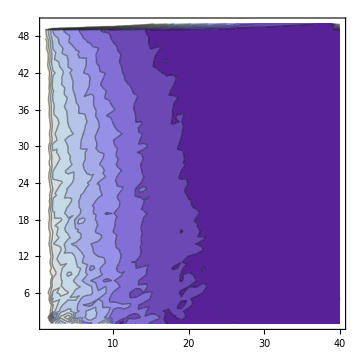
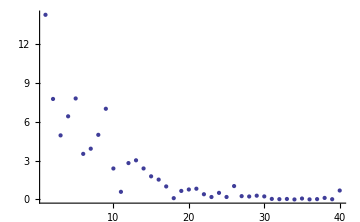

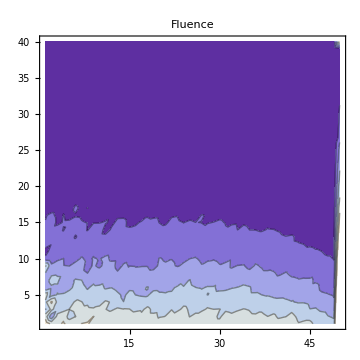
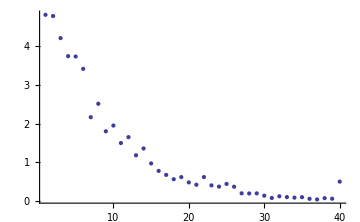

100000 Fotones

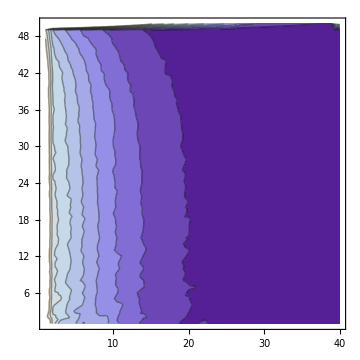
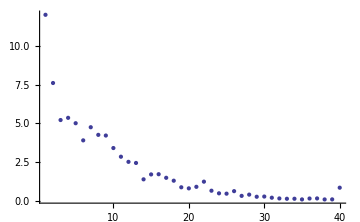

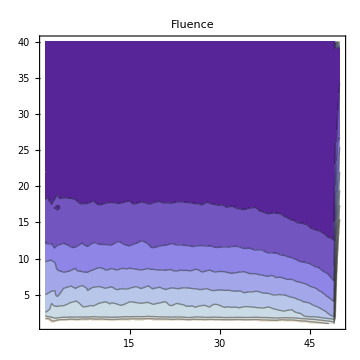
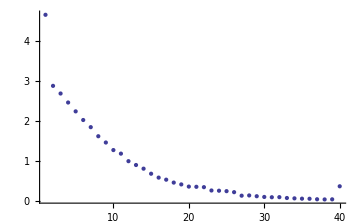

200000 Fotones

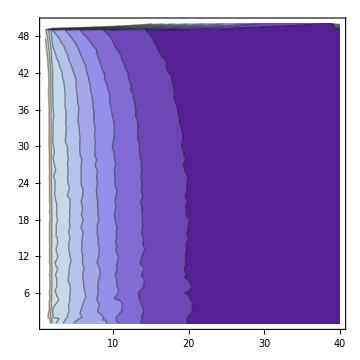
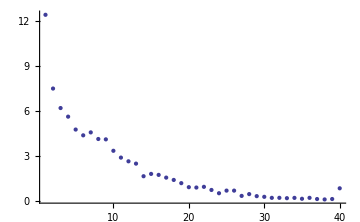

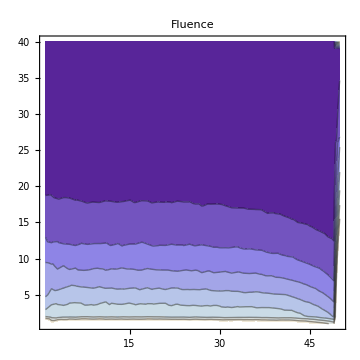
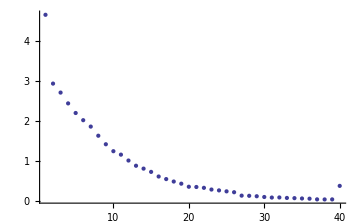

300000 Fotones

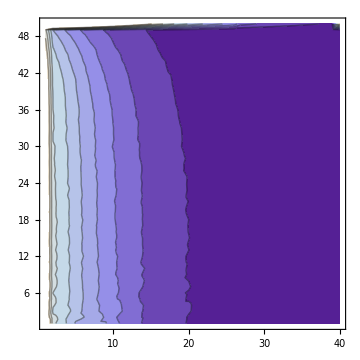
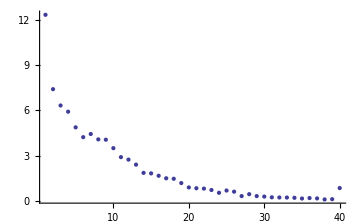

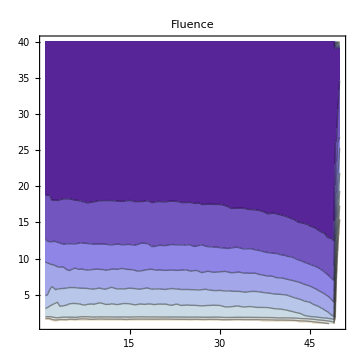
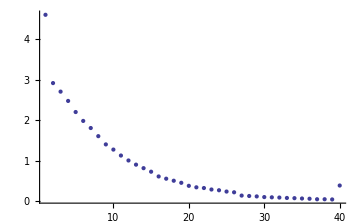

400000 Fotones

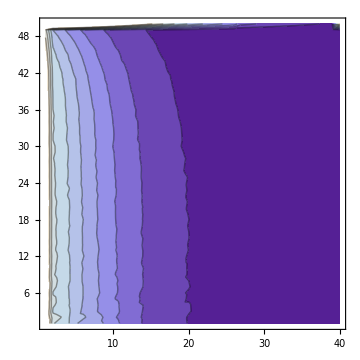
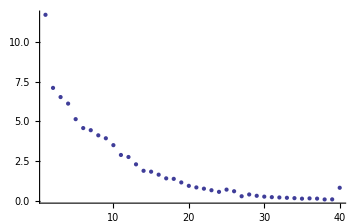

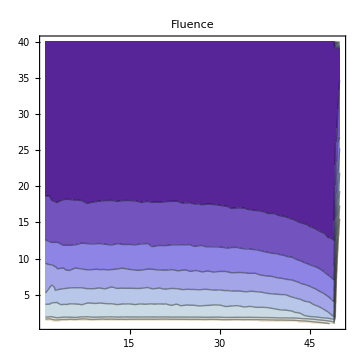
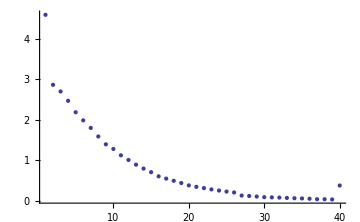

500000 Fotones

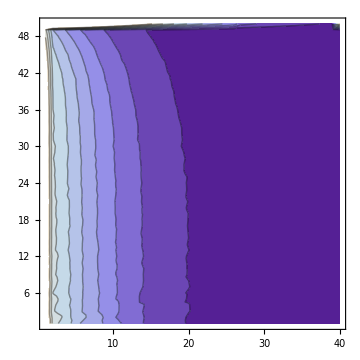
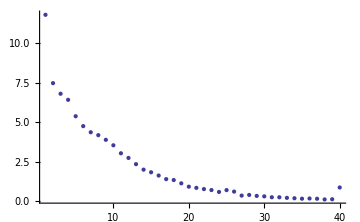

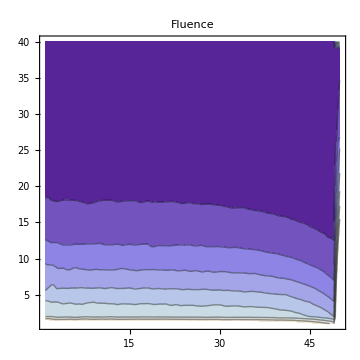
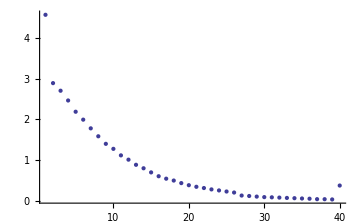

600000 Fotones

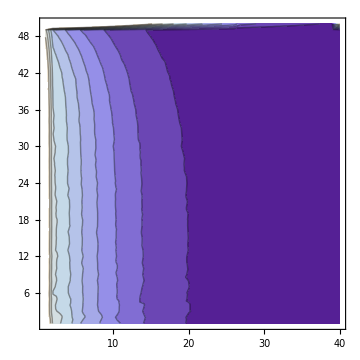
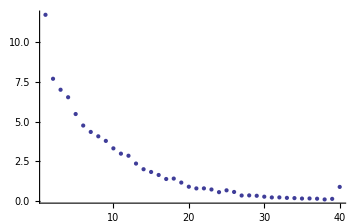

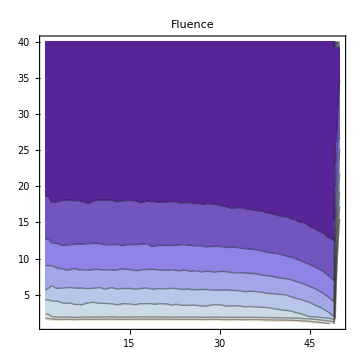
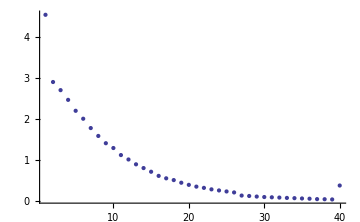

700000 Fotones

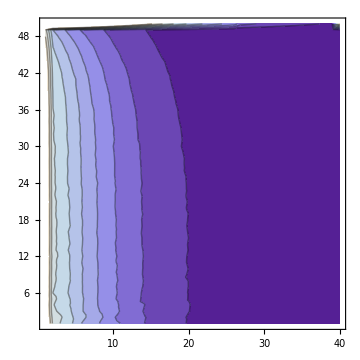
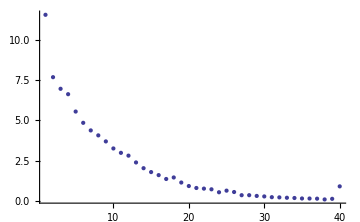

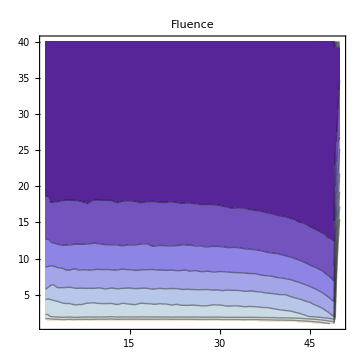
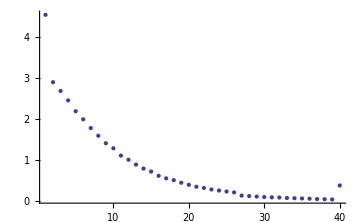

800000 Fotones

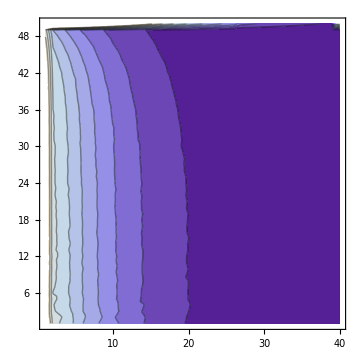
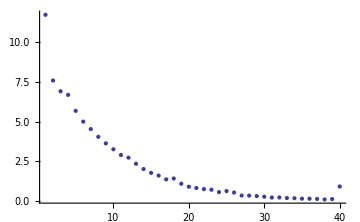

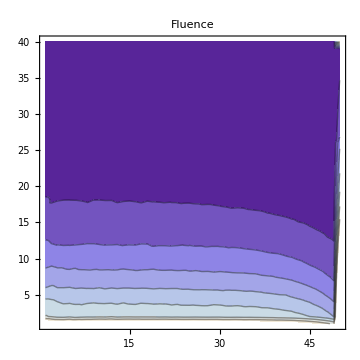
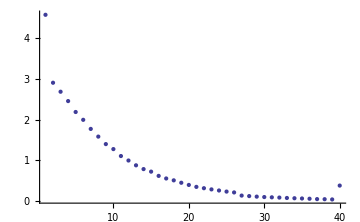

900000 Fotones

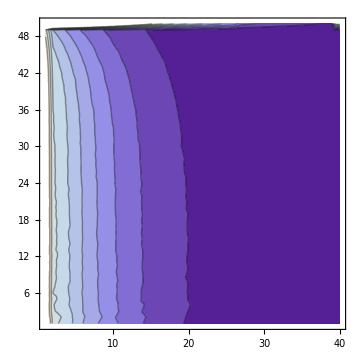
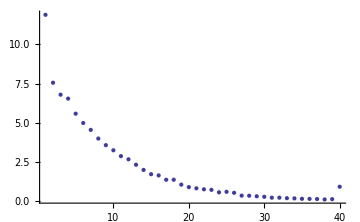

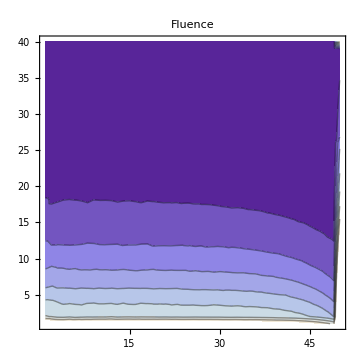
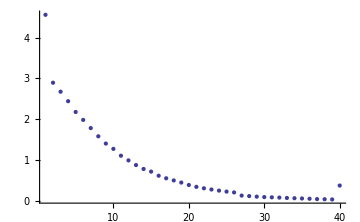

1000000 Fotones

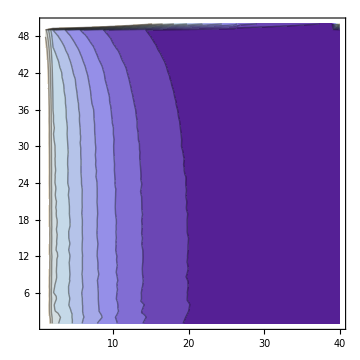
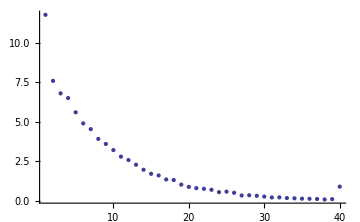

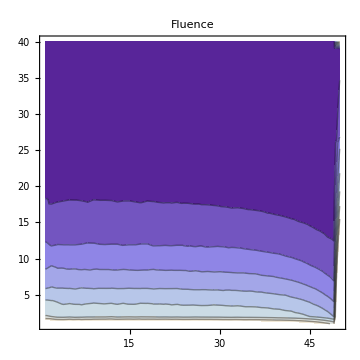
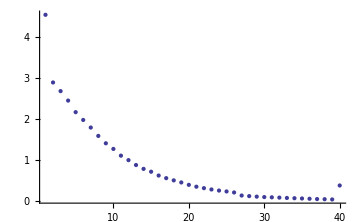

```mathematica
For[i=1,i≤100,i++,
Find[out,"A[nr-1][0]"];
Read[out,Word];
"Numero de photones";
photons=Read[out,Number];
Arz={};
ϕ={};
l=1;
"Leyendo los valores de Arz, guardandolos y normalizando" ;
"Arz/(ΔV N_fotones) ";
For[j=1,j≤ Nr,j++,
AppendTo[Arz,ReadList[out,Number,Nz]/(2 π dr^2 dz(j-0.5) photons )]
];
"Graficos de Arz";
"Calculando la fluencia ϕ=Arz/μa";
k=1;
For[j=1,j<=Nz,j++,
AppendTo[ϕ,Arz[[All,j]]/layers[[k,1]]];
If[i==zlayer[[k]],k++]
];
"Graficos de ϕ";
If[(Divisible[photons,100000]||photons==10000),
Print[photons," Fotones"];
Print[ListContourPlot[Arz,ImageSize->Medium],ListPlot[Arz[[1]],ImageSize->Medium]];
Print[ListContourPlot[ϕ,ImageSize->Medium,PlotLabel->"Fluence"],ListPlot[ϕ[[All,10]],ImageSize->Medium]]
]
]
```